λ = 3.23

1 - NA = 0.00187583 +/- 0.0000960869 (5.12237 %)

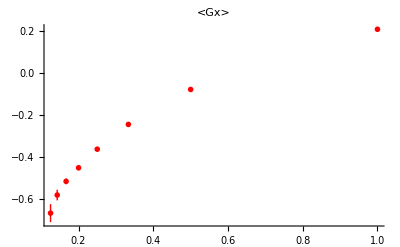

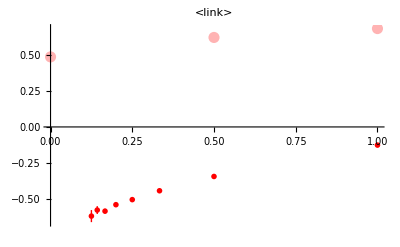

```mathematica
MaxOrder = 8;
GetConvergenceData[fname_,ocol_,dcol_,add_,norm_]:=Module[{oX,oX2,np,FData,i, io,Res,mX,eX},
(* Exporting the data *)
oX=Table[0,{io,1,MaxOrder}];
oX2=Table[0, {i0,1,MaxOrder}];
np=Table[0, {i0,1,MaxOrder}];
FData=Import[fname,"Table"];
(*oXh=Table[{},{io,1,MaxOrder}];*)
For[i=1,i≤Length[FData],i++,
io=FData[[i,ocol]]+1;
np[[io]]++;
oX[[io]]+=FData[[i,dcol]];
oX2[[io]]+=FData[[i,dcol]]^2;
];
Res={};
For[io=1,io≤MaxOrder,io++,
If[np[[io]]>1,
mX=oX[[io]]/np[[io]];
eX=√((oX2[[io]]/np[[io]]-mX^2)/(np[[io]]-1));
AppendTo[Res,{N[1/io],add +norm mX,norm eX}];
];
];
Res
];
(* Useful functions for plotting *)
Needs["ErrorBarPlots`"];
PlotWithErrors[data_,col_]:=Module[{DataToPlot,i},
DataToPlot=Table[{{data[[i,1]],data[[i,2]]},ErrorBar[data[[i,3]]]},{i,1,Length[data]}];
ErrorListPlot[DataToPlot,PlotStyle->{col,PointSize[0.01]},PlotRange->{{0.0,All},{0.0,All}}]
];
(* Useful functions for formatting *)
fsndig[x_,n_]:=ToString[PaddedForm[x,{n+2,n},NumberPadding->{"","0"}]];
(* Set of lattice parameters *)
lambdas={5.0, 4.0, 3.57, 3.45, 3.33, 3.23};
SourceNorms={0.0, 0.0,0.0,0.0,0.0,0.2733377};
VRdata={0.781, 0.708, 0.6499, 0.62134, 0.56809, 0.51202};
O0data={0.5577,0.6270,0.6590,0.66821,0.6775,0.6853};
O1data={0.4541,0.5464,0.5888,0.6009,0.6131,0.6234};
IncData={True,True,True,True,True,True};
(* Forming lists and plotting *)
GxPlots={}; mlPlots={};
For[iλ=1,iλ≤Length[lambdas],iλ++,
λ=lambdas[[iλ]];
c=(iλ-1)/(Length[lambdas]-1);
Color1=RGBColor[c,0,1-c];
Color2=RGBColor[0.7+0.3c,0.7,0.7+0.3(1-c)];
(* Generating file names *)
ScalarFileName="G:\\LAT\\sd_metropolis\\data\\stereo_sm\\scalars_d2_t32_s32_l"<>fsndig[λ,4]<>".dat";
MeanNAFileName="G:\\LAT\\sd_metropolis\\data\\stereo_sm\\mean_nA_d2_t32_s32_l"<>fsndig[λ,4]<>".dat";
If[FileExistsQ[ScalarFileName] && FileExistsQ[MeanNAFileName],
Print["λ = ",λ];
MeanNAData=Transpose[Import[MeanNAFileName,"Table"]][[1]];
MeanNA=Mean[MeanNAData]; ErrNA=√(Variance[MeanNAData]/(Length[MeanNAData]-1));
Print["1 - NA = ",MeanNA," +/- ",ErrNA," (", 100.0 ErrNA/MeanNA," %)"];
GxData=GetConvergenceData[ScalarFileName,1,2,1,1/MeanNA];
MeanLinkData=GetConvergenceData[ScalarFileName,1,4,1,1/MeanNA];
MeanLinkExactData={{0.0,1-VRdata[[iλ]]},{0.5,O1data[[iλ]]},{1.0,O0data[[iλ]]}};
GrGx=Show[PlotWithErrors[GxData,Color1],PlotLabel->"<Gx>"];
GrExact=ListPlot[MeanLinkExactData,PlotStyle->{Color2,PointSize[0.02]},PlotRange->{{0.0,All},{0.0,All}}];
Grml=Show[GrExact,PlotWithErrors[MeanLinkData,Color1],PlotLabel->"<link>",DisplayFunction->$DisplayFunction];
If[IncData[[iλ]],
AppendTo[GxPlots,GrGx];
AppendTo[mlPlots,Grml];
];
];
];
Show[GxPlots,PlotRange->All]
Show[mlPlots,PlotRange->All]
```

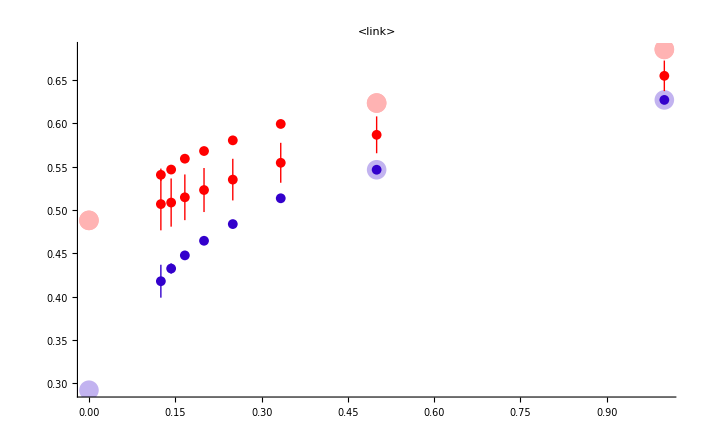

```mathematica
Show[mlplots0,mlplots1]
```

```mathematica
(* Strong- and weak-coupling series for LS=4,D=1 *)
N[1-(3λ)/16-λ^2/256-(5 λ^3)/8192-(33 λ^4)/262144-(63 λ^5)/2097152/.{λ->8/π}]
N[1/λ+1/λ^3+5/λ^7/.{λ->8/π}]
N[1/λ+1/λ^3/.{λ->8/π}]
```

0.30879

0.340636

0.339273

```mathematica
N[]
```

```mathematica
N[-1/(8β)+β+(√(3β)Cot[1/3 ArcSin[3 √3 β^(3/2)]])/(8 √(1-27 β^3))-(2 √(3β)Cos[1/3 ArcSin[3 √3 β^(3/2)]] Sin[1/3 ArcSin[3 √3 β^(3/2)]]^3)/(√(1-27 β^3))/.{β->1/3.00001}]
```

0.458331